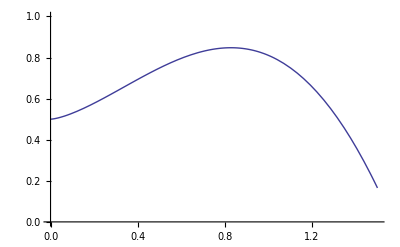

```mathematica
Plot[(Sqrt[x^3]+0.5)*Cos[x],{x,0,1.5},PlotRange->{{0,1.5},{0,1}},Filling->{1}]
```

```mathematica
f[x_]:=(Sqrt[x^3]+0.5)*Cos[x]
```

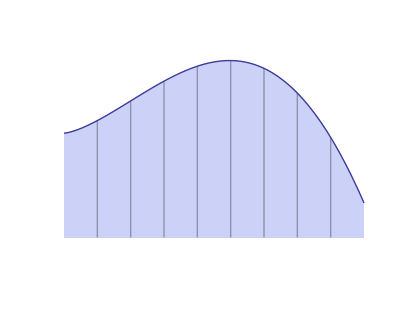

```mathematica
P=RegionPlot[0<y<f[x],{x,0,1.5},{y,-0.15,1},AxesOrigin->{0,0},Frame->False,Mesh->8,MeshFunctions->{#1&},BoundaryStyle->None,Axes->Automatic,AspectRatio->0.8,AxesLabel->{z,"ϕ(t,z)"}]~Show~Plot[f[x],{x,0,1.5},PlotStyle->Thick]
```

```mathematica
G=Graphics[{{Text[Style[j-1,Medium],{1.5/8*3,-0.1}]},
{Text[Style[j,Medium],{1.5/8*4,-0.1}]},
{Text[Style[j+1,Medium],{1.5/8*5,-0.1}]}}];
```

```mathematica
delta=0.08;
ord=0.3;
centre=-1.5/16;
G1=Graphics[{
Arrow[{{1.5/8*4+delta+centre,ord},{1.5/8*4-delta+centre,ord}}],
Arrow[{{1.5/8*5-delta+centre,ord},{1.5/8*5+delta+centre,ord}}]
}];
```

```mathematica
G2=Graphics[{
{Text[Style[Overscript[Subscript[F, j+1/2], n],Medium],{1.5/8*5+centre,ord+0.09}]},
{Text[Style[Overscript[Subscript[F, j-1/2], n],Medium],{1.5/8*4+centre,ord+0.09}]}
}];
```

```mathematica
G3=Graphics[{
Disk[{1.5/8*4,f[1.5/8*4]},0.016],
Text[Style[Subscript[ϕ, j],Medium],{1.5/8*4,f[1.5/8*4]-0.09}]
}];
```

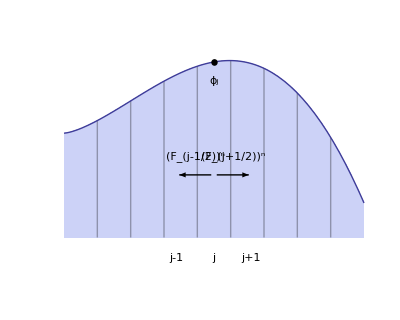

```mathematica
P~Show~G~Show~G1~Show~G2~Show~G3
```